```mathematica
Clear["Global`*"];
```

```mathematica
c=3 10^8;(* м/с *)
NN=300;(* ppm *)
NN=6.62 10^22× NN;(* 1/м^3 *)
h=6.63 10^-34;(* Планк *)
σ=2.5×10^-24;(* сечение перехода, м^2*)
Aeff=Pi/4×7^2×10^-12;(* Эффективная площадь модыб м^2 *)
L=3;(* Длина усилителя, м *)
λ = 1064×10^-9; (* Длина волны, м *)
```

```mathematica
Step[E0_,τ0_,t_] := (E0/((h c)/λ))×UnitBox[t/τ0]/τ0;
Lorenz[E0_,τ0_,t_] := (E0/((h c)/λ))×(τ0/Pi)/(t^2+τ0^2);
Gauss[E0_,τ0_,t_] := (E0/((h c)/λ))×1/(τ0 Sqrt[Pi/2])×Exp[(-2 t^2)/τ0^2];
```

```mathematica
E0var = N[1×10^-9];
τ0var = N[1×10^-12];
n0[t_]:=Gauss[E0var,τ0var,t];
PercentN2ToAbsoluteΔ[percent_] := (2×percent/100-1)×NN;
AbsoluteΔToPercentN2[absolute_] := 100×(1/2+absolute/(2 NN));
Δ0[x_] := PercentN2ToAbsoluteΔ[60];
```

```mathematica
n[x_,t_] := n0[t-x/c]/(1-(1-Exp[-σ (∫_0^x Δ0[u]ⅆu)])×Exp[-2σ c(∫_(-∞)^(t-x/c) n0[u]ⅆu)]);
Δ[x_,t_] :=(Δ0[x]×Exp[-σ (∫_0^x Δ0[u]ⅆu)])/(Exp[2σ c(∫_(-∞)^(t-x/c) n0[u]ⅆu)]+Exp[-σ (∫_0^x Δ0[u] ⅆu)]-1);
nStep[x_,t_,n0_,Δ0_,τ_] := Piecewise[{{n0/(1-(1-Exp[-σ Δ0 x])×Exp[-(2 σ n0 c τ (t - x/c))/τ]),0≤t-x/c≤τ}},0];
```

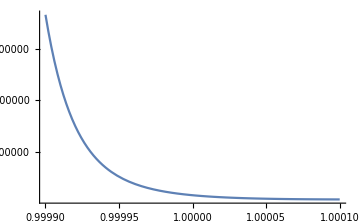
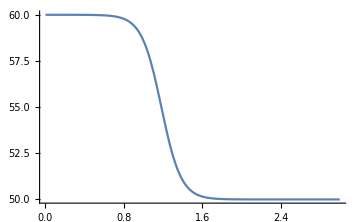
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Plot[n0[t],{t,-τ0var,+τ0var},PlotRange->All,ImageSize->Medium,Exclusions->None],
Plot[n[L,t],{t,L/c-τ0var,L/c+τ0var},PlotRange->All,ImageSize->Medium,Exclusions->None],
Plot[n[L,t]/Max[n0[t-L/c],1],{t,L/c-τ0var,L/c+τ0var},PlotRange->All,ImageSize->Medium,Exclusions->None],
Plot[AbsoluteΔToPercentN2[Δ[x,L/c+2×τ0var]],{x,0,L},PlotRange->All,ImageSize->Medium,Exclusions->None]}
```

```mathematica
Qsat=(h c)/λ×Aeff/(2 σ) (* мощность насыщения *)
```

1.43883×10^-6

```mathematica
(* INITIAL *)
pulseFunction[t_] := n0[t]×(h c)/λ;
EnergyFunction=Assuming[Element[t,Reals],N[∫_(-10 τ0var)^(+10 τ0var) pulseFunction[t]ⅆt]];
t0Function= Assuming[Element[t,Reals],N[(∫_(-10 τ0var)^(+10 τ0var) t pulseFunction[t]ⅆt)/EnergyFunction]];
averageWidthFunction =Assuming[Element[t,Reals],N[Sqrt[(∫_(-10 τ0var)^(+10 τ0var) t^2 pulseFunction[t]ⅆt)/EnergyFunction- t0Function^2]]];
Ans = "Power: "<>ToString[EnergyFunction×10^9]<>" mkJ, t0: "<>ToString[t0Function×10^9]<>" mks, width: "<>ToString[averageWidthFunction×10^12]<>" ps"
```

Power: 1. mkJ, t0: 0. mks, width: 0.5 ps

```mathematica
(* AFTERWARDS 1 *)
pulseFunction[t_] := n[L,t]×(h c)/λ;
EnergyFunction=Assuming[Element[t,Reals],N[∫_(L/c-10 τ0var)^(L/c+10 τ0var) pulseFunction[t]ⅆt]];
t0Function=Assuming[Element[t,Reals],N[(∫_(L/c-10 τ0var)^(L/c+10 τ0var) t pulseFunction[t]ⅆt)/EnergyFunction]];
averageWidthFunction =Assuming[Element[t,Reals],N[Sqrt[(∫_(L/c-10 τ0var)^(L/c+10 τ0var) t^2 pulseFunction[t]ⅆt)/EnergyFunction- t0Function^2]]];
Ans = "Power: "<>ToString[EnergyFunction×10^9]<>" mkJ, t0: "<>ToString[t0Function×10^9]<>" mks, width: "<>ToString[averageWidthFunction×10^12]<>" ps"
```

```mathematica
(* AFTERWARDS 2 *)
pulseFunction[t_] := n[L,t]×(h c)/λ;
EnergyFunction=N[∫_(L/c-10 τ0var)^(L/c+10 τ0var) pulseFunction[t]ⅆt];
t0Function=N[(∫_(L/c-10 τ0var)^(L/c+10 τ0var) t pulseFunction[t]ⅆt)/EnergyFunction];
averageWidthFunction =N[Sqrt[(∫_(L/c-10 τ0var)^(L/c+10 τ0var) t^2 pulseFunction[t]ⅆt)/EnergyFunction- t0Function^2]];
Ans = "Power: "<>ToString[EnergyFunction×10^9]<>" mkJ, t0: "<>ToString[t0Function×10^9]<>" mks, width: "<>ToString[averageWidthFunction×10^12]<>" ps"
```